# The Performance War - PC Benchmarking Suite for WL environment

Dali Lai

Timothee Verdier

## CPU BenchMarking

CPU is the main part WL environment use by default, even rendering 3D images. In the project, for the CPU benchmarking session, we will be testing 10 different functions that I think in the end should give a meaningful score and can be handy when comparing to other machines.
Functions will be using parallel processing if available, and also test the single core in that case and take the ratio of parallel : single = 7 :3, since one benefit multicore much more and the other benefits from single core high frequency more.

```mathematica
LaunchKernels[6];
SetAttributes[Timer,{HoldAll}];
SinglePrimee[a_] := Do[If[PrimeQ[q] == True, 1, 0], {q, 0, a}];
ParaPrime[a_] := ParallelDo[If[PrimeQ[q] == True, 1, 0], {q, 0, a}];
Timer[expr_] :=
  Block[
  {result},
  ClearSystemCache[];
  result = AbsoluteTiming[expr];
  Return[result[[1]]]
 ];
```

CPU test set includes: 
FindPI, SinFindPrime, ParaFindPrime, CompileTIme,
EigenTimePara, EigenTimeSing, LinearSysSing, LinearSysPara, TransposeTime, 
RandomsortPara, RandomsortSing, Render3Dtime, NSloveTimePara, NSloveTimeSingle, Cell3DTime
While I set all the tests level to be around 3~7 seconds on my machine since the machine I did this project was quite new and fast compare to other laptops.

```mathematica
TestSet[] := Module[
{
FindPI, SinFindPrime, ParaFindPrime, Amountofpi = 10^7.5, newtonIteration, CompileTIme,
EigenTimePara, EigenTimeSing, LinearSysSing, LinearSysPara, TransposeTime, 
RandomsortPara, RandomsortSing, Render3Dtime, NSloveTimePara, NSloveTimeSingle, Cell3DTime
},

  FindPI = Timer[N[π, 10000000];];
  SinFindPrime = Timer[SinglePrimee[Amountofpi];];
  ParaFindPrime = Timer[ParaPrime[Amountofpi];];
     newtonIteration = Compile[{{z, _Complex}, {n, _Integer}}, Module[{zn = z}, Do[zn = (2 zn + 1/zn^2)/3, {n}];
        If[Re[zn] > 0, 1, If[Im[zn] > 0, 2, 3]]], RuntimeAttributes -> {Listable}, Parallelization -> True];
  CompileTIme = Timer[ArrayPlot[Table[newtonIteration[x + I*y, 25], 
        {y, -5, 5, 2./199}, {x, -5, 5, 2./199}]]];
  
  EigenTimePara = Module[{a, b, m}, Timer[SeedRandom[1]; a = RandomReal[{}, {1500, 1500}]; 
                  b = DiagonalMatrix[RandomReal[{}, {1500}]]; m = a.b.Inverse[a]; 
                  ParallelDo[Eigenvalues[m], {10}]]];
  EigenTimeSing = Module[{a, b, m}, Timer[SeedRandom[1]; a = RandomReal[{}, {1500, 1500}]; 
                  b = DiagonalMatrix[RandomReal[{}, {1500}]]; m = a.b.Inverse[a]; 
                  Do[Eigenvalues[m], {10}]]];
  LinearSysSing = Module[{m, v}, Timer[SeedRandom[1]; m = RandomReal[{}, {5000, 5000}];
                  v = RandomReal[{}, {5000}]; Do[LinearSolve[m, v], {10}]]];
  LinearSysPara = Module[{m, v}, Timer[SeedRandom[1]; m = RandomReal[{}, {5000, 5000}]; 
                  v = RandomReal[{}, {5000}]; ParallelDo[LinearSolve[m, v], {10}]]];
  TransposeTime = Module[{m}, Timer[SeedRandom[1]; m = RandomReal[{}, {8000, 8000}]; 
                  Do[Transpose[m], {10}]]];
  RandomsortPara = Module[{a}, Timer[SeedRandom[1]; a = RandomInteger[{1, 10^10}, {3*10^6}]; 
                  ParallelDo[Sort[a], {10}]]];
  RandomsortSing = Module[{a}, Timer[SeedRandom[1]; a = RandomInteger[{1, 10^10}, {3*10^6}]; 
                  Do[Sort[a], {10}]]];
  Render3Dtime = RepeatedTiming[SphericalPlot3D[1 + Sin[5 ϕ] Sin[10 θ]/10, {θ, 0, 2 π}, {ϕ, 0, 4 π}, 
                  ColorFunction -> (ColorData["Rainbow"][#6] &), 
                  Mesh -> None, PlotPoints -> 200, Boxed -> False, Axes -> False];][[1]];
  NSloveTimePara = RepeatedTiming[Parallelize[NSolve[Sin[z + 
                  Sin[z + Sin[z]]] == Cos[z + Cos[z + Cos[z]]] && -2 < Re[z] < 2 && -2 < Im[z] < 2, z];]][[1]];
  NSloveTimeSingle = RepeatedTiming[NSolve[Sin[z + 
                  Sin[z + Sin[z]]] == Cos[z + Cos[z + Cos[z]]] && -2 < Re[z] < 2 && -2 < Im[z] < 2, z];][[1]];
  Cell3DTime = RepeatedTiming[Graphics3D[Cuboid/@Position[#,1],
                  ImageSize->Full]&/@CellularAutomaton[{30, {2, 1}, {2, 2,2}},{{{{1}}},0},30];][[1]];
  
  
  <|"PITime" -> FindPI, "FindPrimeSingle" -> SinFindPrime, 
  "FindPrimePara" -> ParaFindPrime, 
  "CompileTime" -> CompileTIme, 
  "EigenTimePara" -> EigenTimePara, 
  "EigenTimeSingle" -> EigenTimeSing, "LinearSystemSingle" -> LinearSysSing, 
  "LinearSystemPara" -> LinearSysPara, "TransposeTime" -> TransposeTime, 
  "SortRandomPara" -> RandomsortPara, "SortRandomSingle" -> RandomsortSing, 
  "Render3DTime" -> Render3Dtime, "NSloveTimePara" -> NSloveTimePara, 
  "NSloveTimeSingle" -> NSloveTimeSingle,
  "Cell3DTime" -> Cell3DTime
  
  |>
  ]
```

Below is the formula used for changing time to score.

```mathematica
Score[t_]:=-900*ArcTan[0.02*t]+900;
```

Notice the function isn’t linear but is somewhat reasonable as I think if one machine takes unreasonable amount of time to finish one task, it should be punished.
Potential issue: Hard to tell the difference in terms of performance since it’s not linear curve.
Advantage: Will know exactly above what score the machine is consider “super decent”, and as the points increases, the value of one point increases as well.
It’s like SAT, improving from 750 to 800 is always harder than from 600 to 700.

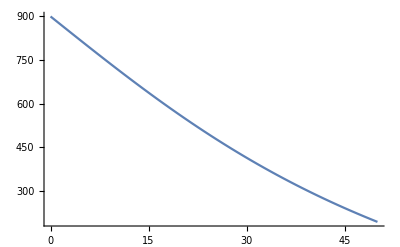

```mathematica
Plot[-900*ArcTan[0.02x]+900,{x,0,50},PlotRange->All,AxesOrigin->{0,0}]
```

Below is the part to add and weight the score of each task and combine them together.

```mathematica
CPUScore:= (
CPUTestResult=TestSet[];
Score[CPUTestResult["PITime"]]+

(3*Score[CPUTestResult["FindPrimeSingle"]]+7*Score[CPUTestResult["FindPrimePara"]])/10+
Score[CPUTestResult["CompileTime"]]+

(3*Score[CPUTestResult["EigenTimeSingle"]]+7*Score[CPUTestResult["EigenTimePara"]])/10+
(Score[CPUTestResult["LinearSystemSingle"]]+Score[CPUTestResult["LinearSystemPara"]])/2+
Score[CPUTestResult["TransposeTime"]]+

(7*Score[CPUTestResult["SortRandomPara"]]+3*Score[CPUTestResult["SortRandomSingle"]])/10+

Score[CPUTestResult["Render3DTime"]]+Score[CPUTestResult["Cell3DTime"]]+

(7*Score[CPUTestResult["NSloveTimePara"]]+3*Score[CPUTestResult["NSloveTimeSingle"]])/10)
```

```mathematica
CPUScore
```

7953.84

## RAM BenchMarking

This task is for testing ram speed, ram speed is usually not stated as MB/sec, but in MHz since the real speed needs to factor in timing and channel used, but for this task it will appear it in MB/sec since this is the apparent speed measured using this method. 
Notice the RAMScore is very insignificant, which is true as well in real life applications, many experiments had shown that.

```mathematica
RAMSpeedTest[] := Module[{
AA,A,B,CC,AASize={2000,2000},ASize={5000,5000},
BSize={10000,10000},CCSize={15000,15000},Speed,Time,Score
},
Speed=UnitConvert[Quantity[
D[Fit[{
{RepeatedTiming[AA=ConstantArray[0.,AASize]][[1]],ByteCount[AA]},
{RepeatedTiming[A=ConstantArray[0.,ASize]][[1]],ByteCount[A]},
{RepeatedTiming[B=ConstantArray[0.,BSize]][[1]],ByteCount[B]},
{RepeatedTiming[CC=ConstantArray[0.,CCSize]][[1]],ByteCount[CC]}},
{1,x},x],x],
"Bytes"/"Seconds"],"Megabytes"/"Seconds"];

ClearAll[A,B,CC,AA];
Score=QuantityMagnitude[Speed]/10;
<|"RAMSpeed" -> Speed,"RAMScore" -> Score|>
]
```

```mathematica
RAMSpeedTest[]
```

<|RAMSpeed→2000. MB/s,RAMScore→200.|>

Since speed isn’t important as much as the amount of total RAM on one machine, factoring in the total amount of RAM available in one’s machine and score it I think will be meaningful in terms of benchmarking the machine.

```mathematica
RAMMuch[]:=
Module[{Weight=350,HowMuch,Score},
Score=Weight*Sqrt[
QuantityMagnitude[HowMuch=SystemInformation["Machine","PhysicalTotal"]]]
;
<|"RAMScore" -> Score,"RAMTotal" -> HowMuch|>
]
```

```mathematica
RAMMuch[]
```

<|RAMScore→1395.65,RAMTotal→15.9008 GiB|>

Total points that the RAM scored.

```mathematica
RAMScore:=(RAMMuch[]["RAMScore"]+RAMSpeedTest[]["RAMScore"])
```

```mathematica
RAMScore
```

1581.54

## Disk BenchMarking

This part is for disk benchmarking, disk speed is usually consider more important than RAM speed (but slower of course) in terms of performance, and usually the amount of disk available isn’t an issue since it’s hard to have one program export an 100+ GB file, the situation is reverse compare to RAM here. 
Although, the speed got from the below test doesn’t really 	agree on a real disk benchmarking software, but it indeed is testing disk speed so just see it as “apparent speed” instead and change it to points, as long as it scales as the real speed increases, this score should still be meaningful.

```mathematica
DiskSpeed[] := Module[
	{
	strLength = 500000000, str, testfile,
	diskwritetime, diskreadtime, diskwritespeed,
	diskreadspeed
	}
	,
	str = StringJoin[ConstantArray["0", strLength]];
	testfile = CreateFile[];
	diskwritetime = First@AbsoluteTiming[WriteString[testfile, str]];
	diskreadtime = First@RepeatedTiming[ReadString[testfile]];
	
	diskwritespeed = UnitConvert[
		Quantity[ByteCount[str]/diskwritetime, "Bytes"/"Seconds"],
		"Megabytes"/"Seconds"
		];
	diskreadspeed = UnitConvert[
		Quantity[ByteCount[str]/diskreadtime, "Bytes"/"Seconds"],
		"Megabytes"/"Seconds"
		];
	
	<|"ApparentDiskWriteSpeed" -> diskwritespeed, "ApparentDiskReadSpeed" -> diskreadspeed|>
]
```

Reasonable amount of points scored on this disk benchmarking, this should be more important than the score from RAM Speed, which it is in this formula.

```mathematica
DiskScore:=QuantityMagnitude[(DiskSpeed[]["ApparentDiskWriteSpeed"]+DiskSpeed[]["ApparentDiskReadSpeed"])]
```

```mathematica
DiskScore
```

616.327

## GPU BenchMarking

GPU isn’t really being used in normal functions in WL environment besides training neutral network. But it is a big part of the PC and as the usage of training neutral network increases, GPU will play a huge role.
Since the machine I used for doing this project supports CUDA (RTX 2070 max-Q) but not OpenCL, we will be testing CUDA functions instead and give a good estimate for GPU performance. 

Test set includes: CUDADot, CUDATranspose, NetTrain for dot operation, convolution and image training from example data. 
To truly test the GPU performance, one should run a test approximately 10 min to actually differentiate a noticeable difference, otherwise, the score for 2 decent GPUs will have quite a close score.

```mathematica
Needs["CUDALink`"];
CUDAResourcesInstall["<path_to_paclet>", Update->True];
GPUTest[]:=Module[
{
A,B,randomsize={8000,8000},dottime,transposetime,foot,
nettest,convNet,dottrainingData,convtrainingData,dottrained,
dottraintime,convtime,convtrained,randomobject,
trainingDataforimage,classesforimage,moduleforimage,
netforimage,timeforimage,trainedimage

},
A=RandomReal[{-50,50},randomsize];
B=RandomReal[{-50,50},randomsize];
dottime=RepeatedTiming[CUDADot[A,B];][[1]];
foot=Entity["AnimalAnatomicalStructure","LeftForefoot::CanisLupusFamiliaris::4t62p"];
transposetime=RepeatedTiming[CUDATranspose/@ColorSeparate[
	AnatomyPlot3D[{foot}]];][[1]];
nettest=NetChain[{100,BatchNormalizationLayer[],Ramp,
	300,BatchNormalizationLayer[],Ramp,300,Ramp,45,Ramp,90},
	"Input"->{80,80}];
convNet=NetChain[{ConvolutionLayer[16,3],
	BatchNormalizationLayer[],Ramp,ConvolutionLayer[32,3],
	BatchNormalizationLayer[],Ramp,ConvolutionLayer[64,3],
	BatchNormalizationLayer[],Ramp,ConvolutionLayer[17,3],
	AggregationLayer[Max]},"Input"->{80,80}];
dottrainingData=<|"Input"->RandomReal[1,{1000,80,80}],
	"Output"->RandomReal[{-20,20},{1000,90}]|>;
{dottraintime,dottrained}=RepeatedTiming@NetTrain[nettest,dottrainingData,
	TargetDevice->"GPU",MaxTrainingRounds->120,
	TrainingProgressReporting->None];
convtrainingData=<|"Input"->RandomReal[1,{1000,80,80}],
	"Output"->RandomReal[{-20,20},{1000,17}]|>;
{convtime,convtrained}=RepeatedTiming@NetTrain[convNet,convtrainingData,
	TargetDevice->"GPU",MaxTrainingRounds->120,
	TrainingProgressReporting->None];
randomobject=ResourceObject["CIFAR-10"];
	trainingDataforimage=ResourceData[randomobject,"TrainingData"];
	RandomSample[trainingDataforimage,3];	
	classesforimage=Union@Values[trainingDataforimage];
	moduleforimage=NetChain[{ConvolutionLayer[20,{3,3}],BatchNormalizationLayer[],
	ElementwiseLayer[Ramp],PoolingLayer[{3,3},"PaddingSize"->1]}];	
	netforimage=NetChain[{moduleforimage,moduleforimage,FlattenLayer[],200,Ramp,10,
	SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{32,32}}],
	"Output"->NetDecoder[{"Class",classesforimage}]];
{timeforimage,trainedimage}=RepeatedTiming@NetTrain[netforimage,trainingDataforimage,
	TargetDevice->"GPU",MaxTrainingRounds->2,
	TrainingProgressReporting->None];	
	
<|"CUDADotTime" -> dottime,"CUDATransposeTime" -> transposetime,
"TrainDotTime"-> dottraintime, "TrainConvLayerTime"-> convtime,
"TrainImageTime"-> timeforimage
|>

]
```

```mathematica
GPUTest[]
```

<|CUDADotTime→5.2,CUDATransposeTime→1.2,TrainDotTime→6.1,TrainConvLayerTime→7.36,TrainImageTime→8.27|>

Will be using the same formula used to calculate CPU score.

```mathematica
Score[t_]:=-900*ArcTan[0.02*t]+900;
```

```mathematica
Plot[-900*ArcTan[0.02x]+900,{x,0,50},PlotRange->All,AxesOrigin->{0,0}]
```

-Graphics-

Adding all the score together from 5 tests.

```mathematica
GPUScore:=(GPUTestResult=GPUTest[];
Score[GPUTestResult["CUDADotTime"]]+
Score[GPUTestResult["CUDATransposeTime"]]+
Score[GPUTestResult["TrainDotTime"]]+
Score[GPUTestResult["TrainConvLayerTime"]]+
Score[GPUTestResult["TrainImageTime"]]
)
```

```mathematica
GPUScore
```

3991.76

## Whole PC BenchMarking

Below is the function combining all 4 test set as well as output a report card containing total score, machine name and total time spent for all test sets.

```mathematica
BenchMarkPC[]:=Module[{cpu,ram,disk,gpu,fields,raw,
args,user, time2},
	user=SystemInformation["FrontEnd","MachineName"];
	time2=AbsoluteTiming[
		cpu=CPUScore;
		ram=RAMScore;
		disk=DiskScore;
		gpu=GPUScore;
		][[1]];
	fields={"user","CPU", "Disk","RAM","GPU","Total","time"};
     raw={{user,cpu,disk,ram,gpu,cpu+ram+disk+gpu,time2}};
	args=<|"people"->(AssociationThread[fields->#]&/@raw)|>;
	GenerateDocument["ExampleData/BenchmarkingTemplate.nb",args];
]
```

```mathematica
BenchMarkPC[]
```